sBart ter Haar Romeny | [" bart.terhaarromeny@gmail.com"](mailto:bart.terhaarromeny@gmail.com) | 
NeuroMath:
    Explainable AI from First Principles | 
["Fall 2022: www.neuromath.net"](https://www.neuromath.net)     Eindhoven University of Technology | □ |  " " | -Graphics-

# Auto-encoder

This notebook is based on the book “Introduction to Machine Learning” by Etienne Bernard,
Wolfram Media Inc., 2021 [Reference].

-Graphics-

From Wikipedia: An auto-encoder is a type of artificial neural network used to learn efficient codings of unlabeled data (unsupervised learning). The encoding is validated and refined by attempting to regenerate the input from the encoding. The auto-encoder learns a representation (encoding) for a set of data, typically for dimensionality reduction, by training the network to ignore insignificant data (“noise”).

An autoencoder learns to compress the data while minimizing the reconstruction error.

#### Example: auto-encoder for MNIST data (images of hand-written digits)

We read the 60.000 28^2 small images:

```mathematica
data=ResourceData["MNIST"]
```

The data come in ‘key-value’ pairs, the images are the ‘keys’, the labels are the ‘values’.
We shuffle the data, take only the images, the ‘keys’, and divide them into a training set and a test set:

```mathematica
digits=Keys@RandomSample[data];
{training,test}=TakeList[digits,{50000,10000}];
```

Check:

```mathematica
First[training]
```

-Graphics-

Now we create a chain of neural network layers.
“SELU” is “ScaledExponentialLinearUnit” (see documentation for ElementwiseLayer);
DropoutLayer[0.01] → 1% of the elements is set to zero during training;

```mathematica
net=NetChain[{
FlattenLayer[],
LinearLayer[90],ElementwiseLayer["SELU"],DropoutLayer[0.01],
LinearLayer[30],ElementwiseLayer["SELU"],DropoutLayer[0.01],
LinearLayer[90],ElementwiseLayer["SELU"],DropoutLayer[0.01],
LinearLayer[784],
ReshapeLayer[{1,28,28}]},
"Input"->NetEncoder[{"Image",{28,28},ColorSpace-> "Grayscale"}],
"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"}]
]
```

NetChain[<>]

To visualize the chain with blocks (red means: not yet trained):

```mathematica
NetGraph[net]
```

NetGraph[<>]

```mathematica
convPlot[net]
```

-Graphics3D-

Let us see what it does for a random digit input:

```mathematica
train1=RandomSample[training,1]
```

{-Graphics-}

```mathematica
net[-Graphics-]
```

NetChain::nninit: Cannot evaluate net: unspecified value for array "Weights" of second layer.

$Failed

This was expected: it does not work yet, as the weights are all still empty.
We first must initialize the net with random weights:

```mathematica
netI=NetInitialize[net]
```

NetChain[<>]

```mathematica
netI[-Graphics-]
```

-Graphics-

As the net is not trained yet, we just get noise.

To train the auto-encoder, we add a mean-squared-loss layer , with MSE = 1/n(Σ(y_o-y_i))^2 , which compares the input and the output of the network:

```mathematica
trainingnet=NetGraph[{netI,MeanSquaredLossLayer[]},{{NetPort["Input"],1}->2}]
```

NetGraph[<>]

Here is now the whole net definition of the auto-encoder, ‘wide → narrow → wide’:

```mathematica
trainingnet=NetGraph[{FlattenLayer[],
LinearLayer[90],ElementwiseLayer["SELU"],DropoutLayer[0.01],
LinearLayer[30],ElementwiseLayer["SELU"],DropoutLayer[0.01],
LinearLayer[90],ElementwiseLayer["SELU"],DropoutLayer[0.01],
LinearLayer[784],
ReshapeLayer[{1,28,28}],MeanSquaredLossLayer[]},{1->2->3->4->5->6->7->8->9->10->11->12,{NetPort["Input"],12}->13},"Input"->NetEncoder[{"Image",{28,28},ColorSpace-> "Grayscale"}]]
```

NetGraph[<>]

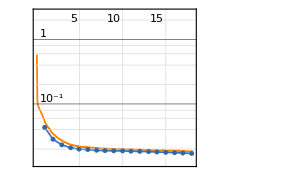
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:14184  rounds:18  time:1.1min  examples/s:14306
data | ,,  training examples:50000  validation examples:10000  processed examples:907776  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.85×10^-2
validation | ,,  loss:1.71×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
results=NetTrain[trainingnet,training,All,ValidationSet->test,MaxTrainingRounds->100,TargetDevice->"GPU"]
```

```mathematica
trainednet=results["TrainedNet"]
```

NetGraph[<>]

The encoder part is formed by the first 6 layers. It generates a feature vector of size 30:

```mathematica
encoder=NetTake[trainednet,6]
```

NetGraph[<>]

```mathematica
encoder[-Graphics-]
```

{0.307801,0.606244,0.475718,0.0397393,0.0882635,0.170607,0.420456,0.309697,0.193689,0.909883,-0.0766467,0.538733,-0.461509,0.476822,0.394755,-0.0319879,0.738599,0.00500173,0.696477,0.0885257,-0.485091,0.237001,0.924068,0.253237,-0.405364,1.11995,0.390589,0.236841,-0.224712,-0.290977}

#### Fun

```mathematica
e3=encoder[-Graphics-];
e4=encoder[-Graphics-];
```

```mathematica
decoder=NetTake[trainednet,{7,12},"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"}]]
```

NetGraph[<>]

```mathematica
Manipulate[decoder[α e3+(1-α)e4],{α,0,1}]
```

#### Autoencoder

Now the network is trained, we can take the 12 layers of the trained net, and attach it before the output layer (which is a decoder generating grayscale images):

```mathematica
autoencoder=NetReplacePart[NetTake[trainednet,12],"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"}]]
```

NetGraph[<>]

It works nicely:

```mathematica
autoencoder[-Graphics-]
```

-Graphics-

On more examples:

```mathematica
MatrixForm[{#,autoencoder[#]}ᵀ]&/@RandomSample[training,10]
```

{(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-)}

## Training the auto-encoder with noisy images

```mathematica
t=#->ImageEffect[#,{"Noise",0.5}] &/@Take[training,10]
```

{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}

We need to include this noise-adding in the auto-encoder pipeline

```mathematica
addnoise=FunctionLayer[#+{RandomReal[{0,0.5},{28,28}]}&,"Input"->NetEncoder[{"Image",{28,28},ColorSpace-> "Grayscale"}],
"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"}]]
```

FunctionLayer[<>]

This function layer gives now the required 28 x 28 noisy image output for a 2D 28 x 28 pixels image input:

```mathematica
ImageAdjust@Image@addnoise[-Graphics-]
```

-Graphics-

The auto-encoder nicely removes the noise:

```mathematica
autoencoder[-Graphics-]
```

-Graphics-

## References

Bernard, E., Introduction to machine learning, Wolfram Media, 2021. ISBN 978-1-57955-048-6 (paperback), 978-1-57955-045-5 (eBook).

#### Functions

```mathematica
layersPlot = Row[{convPlot[#, ImageSize -> 120, BaselinePosition -> Scaled[.8]], #}, Spacer[1]]&;
```

```mathematica
layerColor = {
 ConvolutionLayer -> RGBColor[0.6, 0.7, .9],
 LinearLayer -> RGBColor[1, 0.2, 0.5],
 "Input" -> GrayLevel[.9],
 _ -> GrayLevel[.9]
};
```

```mathematica
ClearAll[convPlot]
convPlot[net_, p: _?NumericQ : 1/3, s: _?NumericQ : 1.2, opts: OptionsPattern[Graphics3D]] :=
Block[
	{layers, layerTypes, output, input, sizes, good, colors, reducer},
	
	layers = Information[net,"Layers"];
	layerTypes = Prepend[Values[Head /@ layers], "Input"];
	
	output = NetExtract[#, "Output"]& /@ layers;
	input = NetExtract[First[layers], "Input"];
	sizes = Replace[Prepend[Values[output], input], 
		{
			x_/;Length[x] == 1 :> Join[x, {1,1}],
			x_/;Length[x] == 0 :> Prepend[{1,1}, x]
		},
		1
	];
	
	good = Position[sizes, x_/;Length[x] == 3, 1];
	{sizes, layerTypes} = Transpose[
		Extract[Transpose[{sizes, layerTypes}], good]
	];
	
	colors = Replace[layerTypes, layerColor, 1];
	
	If[Length[sizes] == 0, Return[Graphics3D[]]];
	
	reducer := Power[#, p]&;
	Graphics3D[
	{
		LightBlue,
		MapThread[
			Function[{color, ch,w,h,pos},
				{color, Cuboid[{pos,-w/2,-h/2}, {pos+ch,w/2,h/2}]}
			],
			{
				colors, 
				reducer@sizes[[All,1]],
				sizes[[All,2]],
				sizes[[All,3]],
				(Accumulate[Prepend[reducer@sizes[[;;-2,1]],0]]) s
			}
		]},
		opts,
		Lighting -> {{"Ambient",White}},
		Boxed -> False
	]
]
```